# MSTW PDF example code

Clear all definitions.

```mathematica
Clear["Global`*"]
```

Load Mathematica package containing global variables and functions to access grids.
Change the pdfpath to the location where the mstwpdf.m file is stored.

```mathematica
pdfpath="/Users/ghmantry/Dropbox/MSTW-PDF-Mathematica-June-2020/mstw2008code";
SetDirectory[pdfpath];
```

```mathematica
<<mstwpdf.m
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
?ReadPDFGrid
```

The function ReadPDFGrid[prefix,ih] reads the PDF grid corresponding to eigenvector set ih, where ih=0 is the central set, into memory from the location specified by prefix.

```mathematica
?xf
```

The function xf[ih,x,q,f] returns x times the parton distribution of flavour f corresponding to eigenvector set ih, where ih=0 is the central set, at a given momentum fraction x and scale q in GeV.  Note that ih and f must be integers, and x and q must be numeric quantities.  The PDG convention is used for the flavour f, that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t.  The valence quark distributions can also be obtained directly with f = 7, 8, 9, 10, 11, 12 corresponding to dv, uv, sv, cv, bv, tv.  The photon distribution is obtained with f = 13.

## Use of the central PDF set

The prefix should be set to the location of the grid files.

```mathematica
prefix=pdfpath<>"/../Grids/mstw2008nlo";
Timing[ReadPDFGrid[prefix,0]]
```

PDF grid read from /Users/ghmantry/Dropbox/MSTW-PDF-Mathematica-June-2020/mstw2008code/../Grids/mstw2008nlo.00.dat

{6.15494,Null}

Write out the central PDFs for a fixed momentum scale x and scale q.

```mathematica
ih=0;x=1.*^-3;q=10.;
upv=xf[ih,x,q,8]
dnv=xf[ih,x,q,7]
usea=xf[ih,x,q,-2]
dsea=xf[ih,x,q,-1]
str=xf[ih,x,q,3]
sbar=xf[ih,x,q,-3]
chm=xf[ih,x,q,4]
cbar=xf[ih,x,q,-4]
bot=xf[ih,x,q,5]
bbar=xf[ih,x,q,-5]
glu=xf[ih,x,q,0]
phot=xf[ih,x,q,13]
```

0.065782

0.034203

0.885658

0.886997

0.72989

0.732202

0.58029

0.58029

0.24099

0.24099

16.535

0.

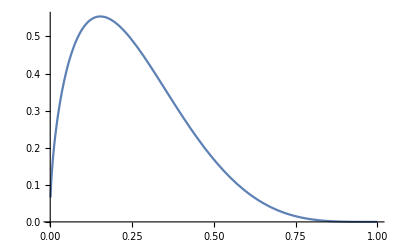

```mathematica
Plot[xf[ih,x,q,8],{x,0.001,1}]
```

## Proton Structure Function

```mathematica
F2[x_,Q2_]:= (2/3)^2*xf[0,x,Sqrt[Q2],2]/x+(1/3)^2*xf[0,x,Sqrt[Q2],1]/x
```

Plot the structure function F2[x, Q2] for different values of Q2. Observe "Bjorken Scaling":

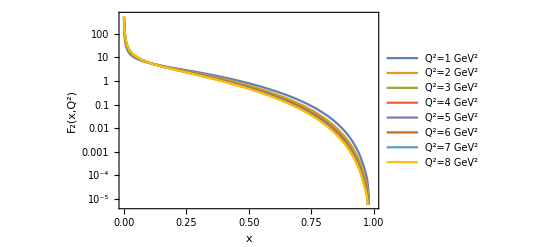

```mathematica
LogPlot[{F2[x,1],F2[x,2],F2[x,3],F2[x,4],F2[x,5],F2[x,6],F2[x,7],F2[x,8]},{x,0.001,1},Frame-> True,FrameLabel-> {"x","F_2(x,Q^2)"},PlotLegends-> {"Q^2=1 GeV^2","Q^2=2 GeV^2","Q^2=3 GeV^2","Q^2=4 GeV^2","Q^2=5 GeV^2","Q^2=6 GeV^2","Q^2=7 GeV^2","Q^2=8 GeV^2"}]
```

#### DIS Cross Section Formula :

Fine structure constant α = e^2/(4*Pi) :

```mathematica
α=1/137
```

1/137

DIS cross section, differential in “x” and “Q^2”:

```mathematica
σ[x_,Q2_,s_]:= (2*Pi*α^2)*F2[x,Q2]/Q2^2*(1+(1-Q2/x/s)^2)
```

```mathematica
σ[0.05,10,90^2]
```

0.0000717709

DIS cross section, differential only in “Q^2”. Obtained by integrating  σ[x,Q2,s] over “x”:

```mathematica
σ[Q2_,s_]:=NIntegrate[σ[x,Q2,s],{x,Q2/s,1}]
```

```mathematica
σ[10,90^2]
```

0.0000186869

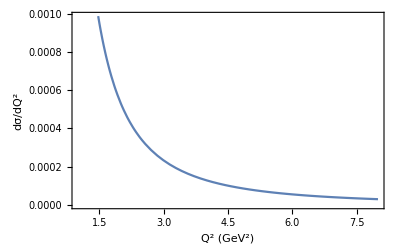

```mathematica
Plot[σ[Q2,90^2],{Q2,1,8},Frame-> True,FrameLabel-> {"Q^2 (GeV^2)", "dσ/dQ^2"}]
```

Next we want a plot of the "normalized" cross section which can be compared with the results of the Pythia simulation...homework for next time!

```mathematica
σtot[Q2min_,Q2max_,s_]:=NIntegrate[(1-Q2/s)(Q2max-Q2min)σ[(1-Q2/s)ζ+Q2/s,Q2,s]/.Q2-> (Q2max-Q2min)ξ+Q2min,{ζ,0,1},{ξ,0,1}]
```

```mathematica
σtot[1,8,90^2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.00184599

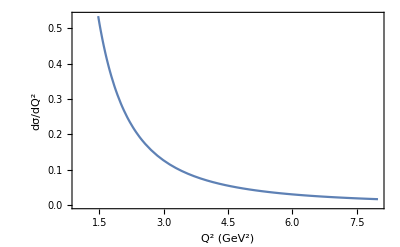

```mathematica
Plot[σ[Q2,90^2]/0.001845993273093831,{Q2,1,8},Frame-> True,FrameLabel-> {"Q^2 (GeV^2)", "dσ/dQ^2"}]
```

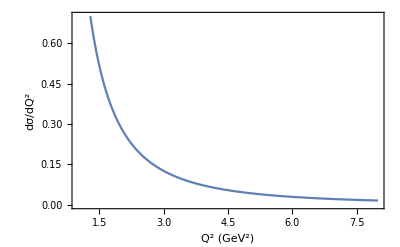

```mathematica
TheoryPlot=Plot[σ[Q2,90^2]/0.001845993273093831,{Q2,1,8},Frame-> True,PlotRange-> {0,0.7},FrameLabel-> {"Q^2 (GeV^2)", "dσ/dQ^2"}]
```